nrmma > Numerical Relativity with NRMMA

# Numerical Relativity in NRMMA

## Getting Started

Load the package

```mathematica
<<nrmma`
```

Set the RunDirectory variable to the directory containing your simulations

```mathematica
(*RunDirectory=$HomeDirectory<>"/Simulations";*)
```

There are many functions in the NRMMA package contains functions for dealing with NR waveforms, BH trajectories, apparent horizons, run statistics, convergence testing and more.

In this tutorial we look at a binary black hole simulation called “bbh” (this is the example simulation which is distributed with NRMMA).

```mathematica
run = "bbh";
```

## Waveforms

ReadPsi4 | Re
Phase | Im
Frequency | Abs

Functions for working with Numerical Relativity waveforms.

Read (2,2) mode of waveform extracted at r=100M from a simulation

```mathematica
psi4=ReadPsi4[run,2,2,100]
```

DataTable[<601>,{{0.,300.}}]

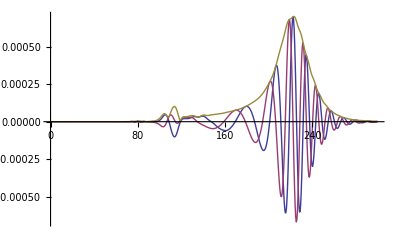

```mathematica
ListLinePlot[{Re[psi4],Im[psi4],Abs[psi4]},PlotRange->All]
```

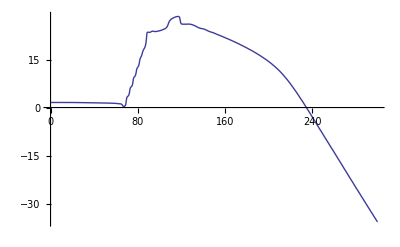

```mathematica
ListLinePlot[Phase[psi4],PlotRange->All]
```

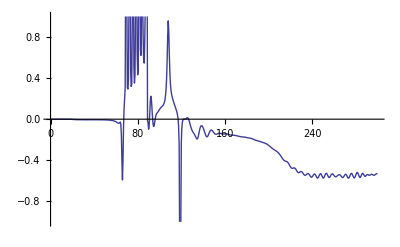

```mathematica
ListLinePlot[Frequency[psi4],PlotRange->{-1,1}]
```

## Trajectories

These functions can be used with output from either PunctureTracker or MinTracker, and the latter could be used to track neutron stars.

ReadBHTrajectory | ReadBHSeparation
ReadBHCoordinates | ReadBHPhase

Functions for dealing with coordinate trajectories.

Puncture 0 trajectory

```mathematica
traj0=ReadBHTrajectory[run,0];
```

```mathematica
Take[traj0,10]
```

{{3,0},{2.99949,0.0115049},{2.99698,0.0615985},{2.99287,0.131566},{2.98756,0.206967},{2.98119,0.281867},{2.9738,0.356226},{2.96542,0.430718},{2.95593,0.505288},{2.94517,0.579732}}

Puncture 1 trajectory

```mathematica
traj1=ReadBHTrajectory[run,1];
```

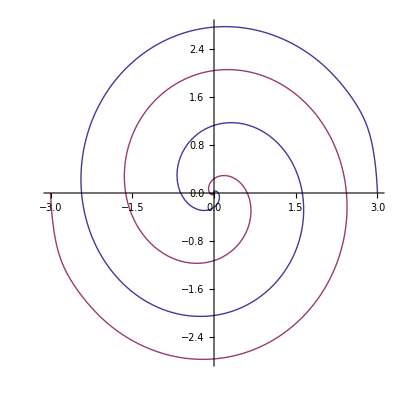

```mathematica
ListLinePlot[{traj0,traj1},PlotRange->All,AspectRatio->1]
```

Separation of the BHs (radius of relative orbit)

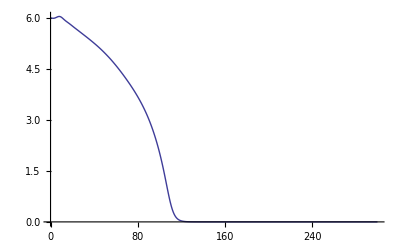

```mathematica
ListLinePlot[ReadBHSeparation[run]]
```

Phase of orbit

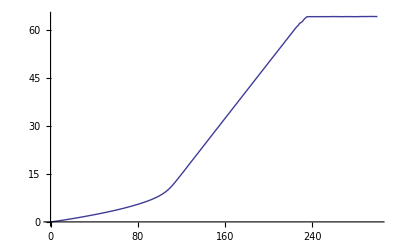

```mathematica
ListLinePlot[ReadBHPhase[run]]
```

Individual coordinates

```mathematica
bh0x=ReadBHCoordinate[run,0,1];
```

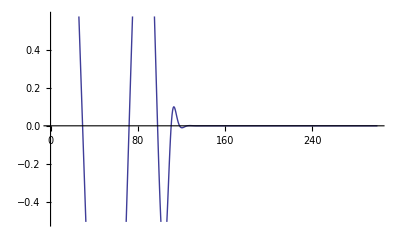

```mathematica
ListLinePlot[bh0x]
```

## Apparent Horizons

Remember that AHFinderDirect numbers its horizons from 1, not 0

Apparent horizon radius

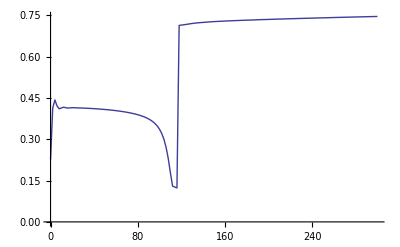

```mathematica
ListLinePlot[ReadAHRadius[run,1]]
```

Apparent horizon mass

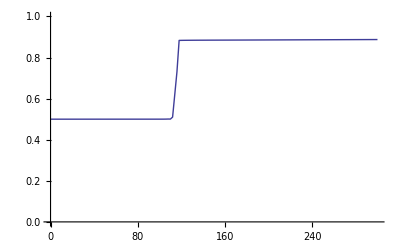

```mathematica
ListLinePlot[ReadAHMass[run,1],PlotRange->{0,1}]
```

## Isolated Horizons

IsolatedHorizon numbers horizons from 0

Spin of the first black hole

```mathematica
spin=ReadIsolatedHorizonSpin[run,0];
Take[ToList[spin],10]
```

{{0,{2.25199×10^-19,-3.71737×10^-20,4.04161×10^-8}},{2,{4.50547×10^-18,3.29458×10^-19,-0.0000206422}},{4,{-3.68054×10^-17,-2.09885×10^-18,-0.0000117056}},{6,{-3.00315×10^-18,5.91561×10^-18,-0.000059465}},{8,{2.53172×10^-18,-1.6196×10^-18,-0.0000295934}},{10,{-1.66584×10^-18,2.15661×10^-18,0.000122601}},{12,{8.44986×10^-19,-3.01987×10^-18,0.000137994}},{14,{-7.92545×10^-19,3.44047×10^-18,0.0000325041}},{16,{-2.29435×10^-17,9.86967×10^-18,0.0000223495}},{18,{9.16704×10^-20,-3.80459×10^-18,0.0000747887}}}

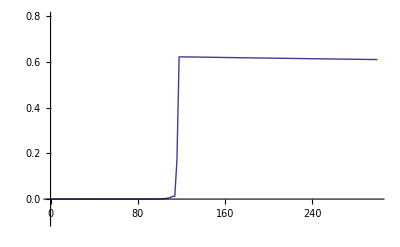

```mathematica
ListLinePlot[Norm[spin],PlotRange->{-0.1,0.8}]
```

RELATED TUTORIALS

CarpetHDF5

DataTable

DataRegion

Kicks